```mathematica
Quit[]
```

## Input

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts-3.11/FeynArts.m"
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

```mathematica
<<"/home/riccardo/Documents/Tesi/ABISS/ABISS.m"
```

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

```mathematica
SetPath[NotebookDirectory[]];
```

Define the process:

```mathematica
SetProcess[{V[1]}->{V[1]}];
```

Generate default Input files

```mathematica
GenerateInput[];
```

Input folder generated in /home/riccardo/Documents/Tesi/TestABISS/BGFSE/input.

Input file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/input/kinematics.m generated.

Input file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/input/integral_families.m generated.

Import the input files (kinematics + integral families).

```mathematica
ImportInput[];
```

Imported input file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/input/integral_families.m.

Imported input file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/input/kinematics.m.

## Diagrams generation

Generate diagrams using feynarts (charged current drell-yan, one loop boxes and born).

```mathematica
SetOptions[InsertFields,  Model -> "/home/riccardo/Documents/Tesi/ABISS/models/SMbgf_Anglerfish", GenericModel ->"Lorentzbgf", InsertionLevel->{Particles}, Restrictions->{NoQuarkMixing,NoLightFHCoupling}, ExcludeParticles-> {}];
```

```mathematica
process={V[1]}->{V[1]};
```

```mathematica
topologies1L=CreateTopologies[1,1-> 1];
```

```mathematica
fields1L=InsertFields[topologies1L, process];
```

Excluding 48 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 15 Particles insertions

Restoring 48 field point(s)

in total: 17 Particles insertions

```mathematica
amp1L=CreateFeynAmp[fields1L];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 15 Particles amplitudes

in total: 17 Particles amplitudes

> Top. 1 ac/bc/cc.m, 0 diagrams

> Top. 2 ac/bd/cdcd.m, 0 diagrams

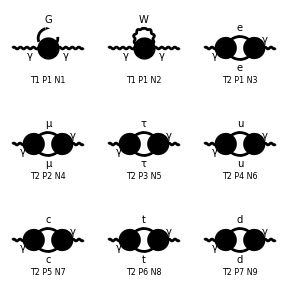

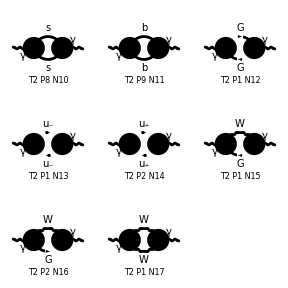

```mathematica
Paint[fields1L];
```

```mathematica
myAmp1L=ExtractAmplitude[amp1L]; (*"Extracts from a FeynArts amplitude a list of amplitudes in the format understood by ABISS."*)
```

```mathematica
SaveAmplitudes[myAmp1L,"OneLoopAmplitudes.m"];
```

Amplitudes saved in /home/riccardo/Documents/Tesi/TestABISS/BGFSE/feynArts_amplitudes/OneLoopAmplitudes.m

```mathematica
Head[myAmp1L]
```

List

## Interference

```mathematica
test=AmpSquare[myAmp1L[[1]],1]//Simplify
test1=AmpSquare[myAmp1L[[2]],1]//Simplify
test2=AmpSquare[myAmp1L[[3]],1]//Simplify
test3=AmpSquare[myAmp1L[[4]],1]//Simplify
test4=AmpSquare[myAmp1L[[5]],1]//Simplify
```

(ⅈ EL^2 gFFAA KiraPropagator[q1,MW] ep[V[1],p1,{Lor1}] SP[{Lor1},{Lor2}] ep^*[V[1],p2,{Lor2}])/(16 π^4)

-1/(8 π^4)ⅈ (-1+d) EL^2 gWWAA KiraPropagator[q1,MW] ep[V[1],p1,{Lor1}] SP[{Lor1},{Lor2}] ep^*[V[1],p2,{Lor2}]

-1/(4 π^4)ⅈ EL^2 gAl^2 KiraPropagator[q1,ME] KiraPropagator[-p2+q1,ME] ep[V[1],p1,{Lor1}] (SP[p2,{Lor2}] SP[q1,{Lor1}]+SP[p2,{Lor1}] SP[q1,{Lor2}]-2 SP[q1,{Lor1}] SP[q1,{Lor2}]-ME^2 SP[{Lor1},{Lor2}]-SP[p2,q1] SP[{Lor1},{Lor2}]+SP[q1,q1] SP[{Lor1},{Lor2}]) ep^*[V[1],p2,{Lor2}]

-1/(4 π^4)ⅈ EL^2 gAl^2 KiraPropagator[q1,MM] KiraPropagator[-p2+q1,MM] ep[V[1],p1,{Lor1}] (SP[p2,{Lor2}] SP[q1,{Lor1}]+SP[p2,{Lor1}] SP[q1,{Lor2}]-2 SP[q1,{Lor1}] SP[q1,{Lor2}]-MM^2 SP[{Lor1},{Lor2}]-SP[p2,q1] SP[{Lor1},{Lor2}]+SP[q1,q1] SP[{Lor1},{Lor2}]) ep^*[V[1],p2,{Lor2}]

-1/(4 π^4)ⅈ EL^2 gAl^2 KiraPropagator[q1,ML] KiraPropagator[-p2+q1,ML] ep[V[1],p1,{Lor1}] (SP[p2,{Lor2}] SP[q1,{Lor1}]+SP[p2,{Lor1}] SP[q1,{Lor2}]-2 SP[q1,{Lor1}] SP[q1,{Lor2}]-ML^2 SP[{Lor1},{Lor2}]-SP[p2,q1] SP[{Lor1},{Lor2}]+SP[q1,q1] SP[{Lor1},{Lor2}]) ep^*[V[1],p2,{Lor2}]

```mathematica
SquareSimplifyAndSave[myAmp1L,{1}]
```

Computed contribution 1-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_1_1.m.

Computed contribution 2-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_2_1.m.

Computed contribution 3-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_3_1.m.

Computed contribution 4-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_4_1.m.

Computed contribution 5-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_5_1.m.

Computed contribution 6-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_6_1.m.

Computed contribution 7-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_7_1.m.

Computed contribution 8-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_8_1.m.

Computed contribution 9-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_9_1.m.

Computed contribution 10-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_10_1.m.

Computed contribution 11-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_11_1.m.

Computed contribution 12-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_12_1.m.

Computed contribution 13-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_13_1.m.

Computed contribution 14-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_14_1.m.

Computed contribution 15-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_15_1.m.

Computed contribution 16-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_16_1.m.

Computed contribution 17-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE//interferences/Contribution_17_1.m.

## Shift

```mathematica
ImportInput[];
```

Imported input file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/input/integral_families.m.

Imported input file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/input/kinematics.m.

```mathematica
ExtractFamily[test]
```

{A0,{MW}}

```mathematica
ExtractFamily[test1]
```

{A0,{MW}}

```mathematica
ExtractFamily[test2]
```

{A0,{ME}}

```mathematica
ExtractFamily[test3]
```

{A0,{MM}}

```mathematica
ExtractFamily[test4]
```

{A0,{ML}}

```mathematica
Do[
ShiftAndSave[i,j,False];
,{i,17},{j,1}]
```

Integral family {A0, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_1_1.m.

Integral family {A0, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_2_1.m.

Integral family {A0, {ME}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_3_1.m.

Integral family {A0, {MM}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_4_1.m.

Integral family {A0, {ML}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_5_1.m.

Integral family {A0, {MU}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_6_1.m.

Integral family {A0, {MC}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_7_1.m.

Integral family {A0, {MT}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_8_1.m.

Integral family {A0, {MD}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_9_1.m.

Integral family {A0, {MS}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_10_1.m.

Integral family {A0, {MB}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_11_1.m.

Integral family {A0, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_12_1.m.

Integral family {A0, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_13_1.m.

Integral family {A0, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_14_1.m.

Integral family {A0, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_15_1.m.

Integral family {A0, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_16_1.m.

Integral family {A0, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/BGFSE/interferences/Contribution_17_1.m.

## Ward identiry test

```mathematica
simplifiedAmp1L=Map[Simplify[AmpSquare[#,1]]&,myAmp1L];
```

```mathematica
simplifiedAmp1L[[3]]
```

-1/(4 π^4)ⅈ EL^2 gAl^2 KiraPropagator[q1,ME] KiraPropagator[-p2+q1,ME] ep[V[1],p1,{Lor1}] (SP[p2,{Lor2}] SP[q1,{Lor1}]+SP[p2,{Lor1}] SP[q1,{Lor2}]-2 SP[q1,{Lor1}] SP[q1,{Lor2}]-ME^2 SP[{Lor1},{Lor2}]-SP[p2,q1] SP[{Lor1},{Lor2}]+SP[q1,q1] SP[{Lor1},{Lor2}]) ep^*[V[1],p2,{Lor2}]

```mathematica
simplifiedAmp1LTot=simplifiedAmp1L/.List->Plus//Simplify
```

1/(16 π^4)ⅈ EL^2 ep[V[1],p1,Lor1] (gFFAA KiraPropagator[q1,MW] SP[Lor1,Lor2]-2 (-1+d) gWWAA KiraPropagator[q1,MW] SP[Lor1,Lor2]+2 gFAW^2 KiraPropagator[q1,MW] KiraPropagator[-p2+q1,MW] SP[Lor1,Lor2]-gFFA^2 KiraPropagator[q1,MW] KiraPropagator[-p2+q1,MW] (SP[Lor1,p2]-2 SP[Lor1,q1]) (SP[Lor2,p2]-2 SP[Lor2,q1])-ggmgmA^2 KiraPropagator[q1,MW] KiraPropagator[-p2+q1,MW] (SP[Lor1,p2]-SP[Lor1,q1]) SP[Lor2,q1]-ggpgpA^2 KiraPropagator[q1,MW] KiraPropagator[-p2+q1,MW] (SP[Lor1,p2]-SP[Lor1,q1]) SP[Lor2,q1]+gWWA^2 KiraPropagator[q1,MW] KiraPropagator[-p2+q1,MW] ((-3+2 d) SP[Lor1,q1] (SP[Lor2,p2]-2 SP[Lor2,q1])+SP[Lor1,p2] (3 SP[Lor2,p1]-(-3+d) SP[Lor2,p2]+(-3+2 d) SP[Lor2,q1])+2 SP[Lor1,Lor2] (SP[p2,q1]-SP[q1,q1]))+4 gAl^2 KiraPropagator[q1,ME] KiraPropagator[-p2+q1,ME] (-SP[Lor1,q1] (SP[Lor2,p2]-2 SP[Lor2,q1])-SP[Lor1,p2] SP[Lor2,q1]+SP[Lor1,Lor2] (ME^2+SP[p2,q1]-SP[q1,q1]))+4 gAl^2 KiraPropagator[q1,ML] KiraPropagator[-p2+q1,ML] (-SP[Lor1,q1] (SP[Lor2,p2]-2 SP[Lor2,q1])-SP[Lor1,p2] SP[Lor2,q1]+SP[Lor1,Lor2] (ML^2+SP[p2,q1]-SP[q1,q1]))+4 gAl^2 KiraPropagator[q1,MM] KiraPropagator[-p2+q1,MM] (-SP[Lor1,q1] (SP[Lor2,p2]-2 SP[Lor2,q1])-SP[Lor1,p2] SP[Lor2,q1]+SP[Lor1,Lor2] (MM^2+SP[p2,q1]-SP[q1,q1]))+4 gAd^2 KiraPropagator[q1,MB] KiraPropagator[-p2+q1,MB] (-SP[Lor1,q1] (SP[Lor2,p2]-2 SP[Lor2,q1])-SP[Lor1,p2] SP[Lor2,q1]+SP[Lor1,Lor2] (MB^2+SP[p2,q1]-SP[q1,q1])) SumOver[Col3,3]+4 gAu^2 KiraPropagator[q1,MC] KiraPropagator[-p2+q1,MC] (-SP[Lor1,q1] (SP[Lor2,p2]-2 SP[Lor2,q1])-SP[Lor1,p2] SP[Lor2,q1]+SP[Lor1,Lor2] (MC^2+SP[p2,q1]-SP[q1,q1])) SumOver[Col3,3]+4 gAd^2 KiraPropagator[q1,MD] KiraPropagator[-p2+q1,MD] (-SP[Lor1,q1] (SP[Lor2,p2]-2 SP[Lor2,q1])-SP[Lor1,p2] SP[Lor2,q1]+SP[Lor1,Lor2] (MD^2+SP[p2,q1]-SP[q1,q1])) SumOver[Col3,3]+4 gAd^2 KiraPropagator[q1,MS] KiraPropagator[-p2+q1,MS] (-SP[Lor1,q1] (SP[Lor2,p2]-2 SP[Lor2,q1])-SP[Lor1,p2] SP[Lor2,q1]+SP[Lor1,Lor2] (MS^2+SP[p2,q1]-SP[q1,q1])) SumOver[Col3,3]+4 gAu^2 KiraPropagator[q1,MT] KiraPropagator[-p2+q1,MT] (-SP[Lor1,q1] (SP[Lor2,p2]-2 SP[Lor2,q1])-SP[Lor1,p2] SP[Lor2,q1]+SP[Lor1,Lor2] (MT^2+SP[p2,q1]-SP[q1,q1])) SumOver[Col3,3]+4 gAu^2 KiraPropagator[q1,MU] KiraPropagator[-p2+q1,MU] (-SP[Lor1,q1] (SP[Lor2,p2]-2 SP[Lor2,q1])-SP[Lor1,p2] SP[Lor2,q1]+SP[Lor1,Lor2] (MU^2+SP[p2,q1]-SP[q1,q1])) SumOver[Col3,3]) ep^*[V[1],p2,Lor2]

## KiraInput

```mathematica
Do[
GenerateAndSaveKiraInput[i,j];
,{i,17},{j,1}]
```

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_1_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_2_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_3_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_4_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_5_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_6_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_7_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_8_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_9_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_10_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_11_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_12_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_13_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_14_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_15_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_16_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/BGFSE/kira_input/Contribution_17_1.m.

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[A0,{MW},1,0],userIntegral[A0,{ME},0,1],userIntegral[A0,{ME},1,0],userIntegral[A0,{ME},1,1],userIntegral[A0,{MM},0,1],userIntegral[A0,{MM},1,0],userIntegral[A0,{MM},1,1],userIntegral[A0,{ML},0,1],userIntegral[A0,{ML},1,0],userIntegral[A0,{ML},1,1],userIntegral[A0,{MU},0,1],userIntegral[A0,{MU},1,0],userIntegral[A0,{MU},1,1],userIntegral[A0,{MC},0,1],userIntegral[A0,{MC},1,0],userIntegral[A0,{MC},1,1],userIntegral[A0,{MT},0,1],userIntegral[A0,{MT},1,0],userIntegral[A0,{MT},1,1],userIntegral[A0,{MD},0,1],userIntegral[A0,{MD},1,0],userIntegral[A0,{MD},1,1],userIntegral[A0,{MS},0,1],userIntegral[A0,{MS},1,0],userIntegral[A0,{MS},1,1],userIntegral[A0,{MB},0,1],userIntegral[A0,{MB},1,0],userIntegral[A0,{MB},1,1],userIntegral[A0,{MW},1,1],userIntegral[A0,{MW},0,1]}

```mathematica
SaveScalarIntegrals["scalar_integrals"];
```

```mathematica
ExportScalarIntegrals["kira_scalar_integrals.dat"];
```

## Apply Kira sub;

```mathematica
ImportScalarIntegrals["scalar_integrals"];
```

```mathematica
PrintRules[]
```

{}

```mathematica
DetermineMasterIntegrals[]
```

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[A0,{MW},1,0],userIntegral[A0,{ME},0,1],userIntegral[A0,{ME},1,0],userIntegral[A0,{ME},1,1],userIntegral[A0,{MM},0,1],userIntegral[A0,{MM},1,0],userIntegral[A0,{MM},1,1],userIntegral[A0,{ML},0,1],userIntegral[A0,{ML},1,0],userIntegral[A0,{ML},1,1],userIntegral[A0,{MU},0,1],userIntegral[A0,{MU},1,0],userIntegral[A0,{MU},1,1],userIntegral[A0,{MC},0,1],userIntegral[A0,{MC},1,0],userIntegral[A0,{MC},1,1],userIntegral[A0,{MT},0,1],userIntegral[A0,{MT},1,0],userIntegral[A0,{MT},1,1],userIntegral[A0,{MD},0,1],userIntegral[A0,{MD},1,0],userIntegral[A0,{MD},1,1],userIntegral[A0,{MS},0,1],userIntegral[A0,{MS},1,0],userIntegral[A0,{MS},1,1],userIntegral[A0,{MB},0,1],userIntegral[A0,{MB},1,0],userIntegral[A0,{MB},1,1],userIntegral[A0,{MW},1,1],userIntegral[A0,{MW},0,1]}

```mathematica
Do[
SaveResult[i,j];
,{i,17},{j,1}]
```